# Beads On a Wire

This is the first version to use a custom-written RK-4, state-space integrator instead of Mathematica's built-in integrator.

## Custom Solution

## Graphical Gadgets

```mathematica
torus[{R_, r_}, {x_,y_,z_}] :=(x^2+y^2+z^2+R^2-r^2)^2==4 R^2(x^2+z^2);
```

```mathematica
ring=ContourPlot3D[ 
Evaluate[torus[{1,.03},{x,y,z}]],
{x,-1.2,1.2},{y,-1.2,1.2},{z,-1.2,1.2},
Mesh->None,
ContourStyle->{RGBColor[1,.71,0],Specularity[White,10]},PlotPoints->100,Boxed->False,Axes->None];
```

```mathematica
frame=Graphics3D[{
Gray,Thick,Line[{
{{0,0,1},{0,0,1.2}},
{{-1.1,0,1.2},{1.1,0,1.2}},
{{0,0,-1},{0,0,-1.2}},
{{-1.1,0,-1.2},{1.1,0,-1.2}}}]}];
```

```mathematica
staticBall[θ_]:=Graphics3D[{
RGBColor[.33,.78,.26],Specularity[White,20],
Sphere[{
Sin[θ],(* Cos[Om a], *)
0,(* Sin[θ[t]/.sol[Om]],(* Sin[Om a], *)*)
-Cos[θ]},
.12]}];
```

```mathematica
ball[angfunc_,Om_,a_,rgb_:RGBColor[.33,.26,.78]]:= Graphics3D[{
rgb,Specularity[White,20],
Sphere[{
(* X *)Sin[angfunc[Om,a]],(* Cos[Om a], *)
(* Y *)0,(* Sin[angfunc[Om,a]],(* Sin[Om a], *)*)
(* Z *)-Cos[angfunc[Om,a]]},
(* r *).12]}];
```

```mathematica
ball2[{x_,y_},rgb_:RGBColor[.33,.26,.78]]:= Graphics3D[{
rgb,Specularity[White,20],Sphere[{x,y,0},(* r *).5]}];
```

```mathematica
ball2[{1,2},{RGBColor[1,2,3]}]
```

-Graphics3D-

```mathematica
minotaur[Om_,a_]:=Graphics3D[{
Text["θ = "<>ToString@theta[1,Om,a],{-.8,0,1}],
Text["θ̇ = "<>ToString@thetaDot[1,Om,a],{.8,0,1}]}];
```

```mathematica
minotaurRK[angFunc_,velFunc_,k_,Om_,a_]:=Graphics3D[{
Text["θ = "<>ToString@angFunc[k,Om,a],{-.8,0,1}],
Text["θ̇ = "<>ToString@velFunc[k,Om,a],{.8,0,1}]}];
```

## Parameters

### Permutations

```mathematica
preps[x_,lls_List]:=Map[
Function[l,Prepend[l,x]],
lls];
```

```mathematica
perms[{}]:={{}};
```

```mathematica
perms[l_List]:=Flatten[
Map[
Function[elt,preps[elt,perms[Complement[l,{elt}]]]],
l],1];
```

### Colors

```mathematica
greenCol=RGBColor[.33,.78,.26];
```

```mathematica
randCol:=RGBColor@@RandomReal[1,3];
```

```mathematica
col1=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col2=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col3=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col4=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col5=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col6=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col7=RGBColor@@RandomSample[{.33,.78,.26}];
```

### Global System Parameters

```mathematica
topΩ=9.6;
incrΩ=0.8;
```

```mathematica
Ωs=Table[i,{i,0,topΩ,incrΩ}]
```

{0.,0.8,1.6,2.4,3.2,4.,4.8,5.6,6.4,7.2,8.,8.8,9.6}

### Per-Bead Parameters

```mathematica
μ=2;
ϵ=0.001; (* unused at present *)
m=1;
R=1;
g=9.8;
lowT=0;
highT=20;
```

### Per-Bead Initial Conditions

```mathematica
θ10=RandomReal[2π];θ1dot0=0;
```

```mathematica
θ20=RandomReal[2π];θ2dot0=0;
```

```mathematica
θ30=RandomReal[2π];θ3dot0=0;
```

```mathematica
θ40=RandomReal[2π];θ4dot0=0;
```

```mathematica
θ50=RandomReal[2π];θ5dot0=0;
```

```mathematica
θ60=RandomReal[2π];θ6dot0=0;
```

```mathematica
θ70=RandomReal[2π];θ7dot0=0;
```

## Custom Integrator

Write differential equations in first-order, state-space form. In particular, Lagrange's equations (or Newton's) look like this

ⅆ/ⅆt[q(t)
q̇(t)]=[0 | 1
F(q,q̇,t) | G(q,q̇,t)][q(t)
q̇(t)]

We can write this in shorthand; let Ψ(t)=[q(t),q̇(t)]^T, Φ(q,q̇,t)=[[0,1],[F(q,q̇,t),G(q,q̇,t)]], then

ⅆ/ⅆt Ψ(t)=Φ(q,q̇,t)Ψ(t)

For instance, consider a spring with constant -k and a damper with constant -ν on a mass m in one dimension. Write the equations as

[q̇(t)
q̈(t)]=[0 | 1
-k/m | -ν/m][q(t)
q̇(t)]

In general, as above, the derivative matrix is a function of the q-vector and of the time, but this one is constant

The following is a completely general, fourth-order Runge-Kutta integrator that takes four arguments:
	ψ: a state vector at any time
	ϕ: a function of ψ and t that returns a state-space matrix as above
	t: the current time
	dt: the interval of time to the next time

To produce a sequence of integrands, just FoldList this over a Range of times, as shown immediately below:

```mathematica
rkStep[ψ_,ϕ_,t_,dt_]:=
Module[{dtk1=dt*ϕ[ψ,t].ψ},
Module[{dtk2=dt*ϕ[ψ+dtk1/2,t+dt/2].(ψ+dtk1/2)},
Module[{dtk3=dt*ϕ[ψ+dtk2/2,t+dt/2].(ψ+dtk2/2)},
Module[{dtk4=dt*ϕ[ψ+dtk3,t+dt].(ψ+dtk3)},
ψ+(dtk1+2dtk2+2dtk3+dtk4)/6]]]]
```

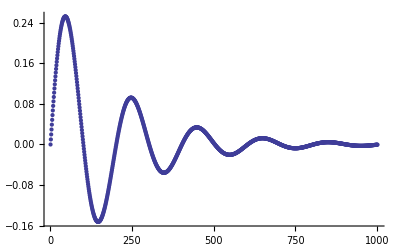

```mathematica
ListPlot[#⟦1⟧&/@
Module[{
m=1, (* mass *)
k=10, (* spring constant *)
ν=1, (* damping constant *)
dt=0.01, (* time step (ansatz) *)
t0=0, (* start time *)
tN=10, (* end time *)
mat, (* matrix in state-space form *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
mat={{0,1},{-k/m,-ν/m}};
ϕ=Function[{ψ,t},mat];(* This time, it's a constant matrix ... *)
FoldList[
rkStep[#1,ϕ,#2,dt]&,(* calculate one step *)
{0,1},(* initial state *)
Range[t0,tN,dt]]]]
```

## Equations of Motion

### Gravitation, Spin, and Damping

```mathematica
gravf[ang_]:=-g m R Sin[ang]
```

```mathematica
spinf[ang_,Ω_]:=m R^2 Ω^2 Cos[ang] Sin[ang]
```

```mathematica
dampf[angVel_]:=-μ R angVel
```

### Electrostatic Repulsion

circumferential component of electrostatic force on thing at θ1 from thing at θ2. thetas have zero point at bottom of ring.

```mathematica
ef[θ1_,θ2_]:=Module[{
x=R Cos[#]&,y=R Sin[#]&,
ψ=θ2-θ1,dx,dy,
dsqrd,fmag,dir,compo,
c1=1,c2=1},
dx=x[θ2]-x[θ1];dy=y[θ2]-y[θ1];dsqrd=dx^2+dy^2;
fmag=c1 c2/dsqrd;
dir=ArcTan[1-Cos[ψ],-Sin[ψ]];
compo=fmag Sin[dir];
compo];
```

```mathematica
repulsef[ψ_,k_,n_]:=
-Sum[ef[ψ⟦i⟧,ψ⟦k⟧],{i,Complement[Range[n],{k}]}]
```

dampf is linear; leave it out of the following:

```mathematica
nonlinf[ψ_,k_,n_,Ω_]:=
gravf[ψ⟦k⟧]+spinf[ψ⟦k⟧,Ω]+repulsef[ψ,k,n]
```

### State-space for the Beads

Let the state of the seven beads on the wire be 7 thetas in a row, and their velocities be seven theta-dots in a row. The state vector [q,q̇], thus has 14 elements, and the state-space matrix is 14×14:

```mathematica
beadsMat[ψ_,Ω_,t_]:={
{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1},{nonlinf[ψ,1,7,Ω]/(m R^2 ψ⟦1⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0,0,0,0},
{0,nonlinf[ψ,2,7,Ω]/(m R^2 ψ⟦2⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0,0,0},
{0,0,nonlinf[ψ,3,7,Ω]/(m R^2 ψ⟦3⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0,0},
{0,0,0,nonlinf[ψ,4,7,Ω]/(m R^2 ψ⟦4⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0},
{0,0,0,0,nonlinf[ψ,5,7,Ω]/(m R^2 ψ⟦5⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0},
{0,0,0,0,0,nonlinf[ψ,6,7,Ω]/(m R^2 ψ⟦6⟧),0,0,0,0,0,0,-μ R/(m R^2),0},
{0,0,0,0,0,0,nonlinf[ψ,7,7,Ω]/(m R^2 ψ⟦7⟧),0,0,0,0,0,0,-μ R/(m R^2)}
}
```

```mathematica
ψlook={.1,.2, .3, .4, .5, .6, .7,0,0,0,0,0,0,0};
```

```mathematica
beadsMat[ψlook, 0, 0.4]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1498.64 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -240.697 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -67.2432 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -9.54075 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 25.157 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 67.7649 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 203.675 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

```mathematica
(Timing[soln=Module[{
dt=0.04, (* time step (ansatz) *)
t0=0, (* start time *)
tN=5, (* end time *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
ϕ=Function[{q,t},beadsMat[q,0,t]];
FoldList[
rkStep[#1,ϕ,#2,dt]&,(* calculate one step *)
{RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],0,0,0,0,0,0,0},(* initial state *)
Range[t0,tN,dt]]]]⟦1⟧//ToString)<>" Seconds to solve."
```

1.841 Seconds to solve.

```mathematica
Length@soln
```

127

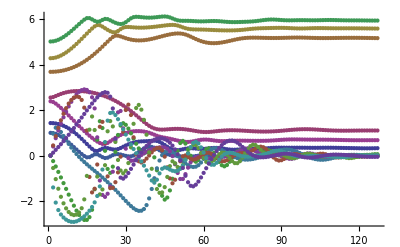

```mathematica
ListPlot[Transpose@soln]
```

```mathematica
Module[{},
Manipulate[
Show[
ring,
frame,
ball[soln⟦#2,1⟧&,0,a,randCol],
ball[soln⟦#2,2⟧&,0,a,col2],
ball[soln⟦#2,3⟧&,0,a,col3],
ball[soln⟦#2,4⟧&,0,a,col4],
ball[soln⟦#2,5⟧&,0,a,col5],
ball[soln⟦#2,6⟧&,0,a,col6],
ball[soln⟦#2,7⟧&,0,a,col7],
minotaurRK[soln⟦#3,#1⟧&,soln⟦#3,7+#1⟧&,1,0,a],
Boxed->True,
Axes->True,
AxesLabel->{"X","Y","Z"},
ViewPoint->{0,-∞,0},PlotRange->1.2,ImageSize->{400,400}],{{a,1,"animate"},1,Length@soln,1,ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->True,AnimationRate->14},
{{a,1,"manual control"},1,Length@soln,1}]]
```

## 3x3 Layout

```mathematica
randomHeightWidth:=RandomReal[1,{2}]
```

```mathematica
threeByThree[heightsAndWidths_List]:=Module[{
maxH,maxW,
centeredUnitSquare=Polygon[{{-1/2,-1/2},{-1/2,1/2},{1/2,1/2},{1/2,-1/2}}],
rectangle},
maxH=Max[Map[#⟦1⟧&,heightsAndWidths]];
maxW=Max[Map[#⟦2⟧&,heightsAndWidths]];
rectangle=Function[{x,y,h,w},
{GeometricTransformation[
GeometricTransformation[
centeredUnitSquare,
ScalingTransform[{w/(3maxW),h/(3maxH)}]],
TranslationTransform[{x,y}]]
}];
Graphics[{(* First, the cage *)
Line[{{0,0},{0,1},{1,1}, {1, 0},{0,0}}],
Line[{{0,1/3},{1,1/3}}],Line[{{0,2/3},{1,2/3}}],
Line[{{1/3,0},{1/3,1}}],Line[{{2/3,0},{2/3,1}}]}
~Join~{Table[rectangle[
(1/2+((i-1)~Mod~3))/3,
(1/2+((i-1)~Quotient~3))/3,
Sequence@@heightsAndWidths⟦i⟧],
{i,9}]}
]]
```

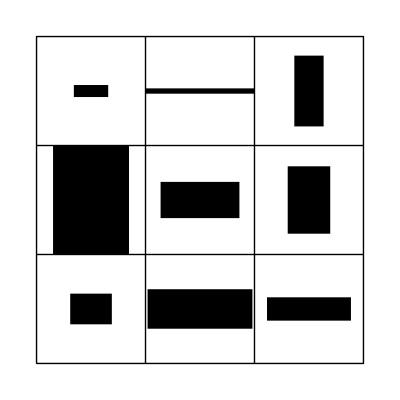

```mathematica
threeByThree[Table[randomHeightWidth,{9}]]
```

```mathematica
f[Sequence@{x,y}]
```

f({x,y})

```mathematica
randomHeightWidth
```

{0.917013,0.723807}

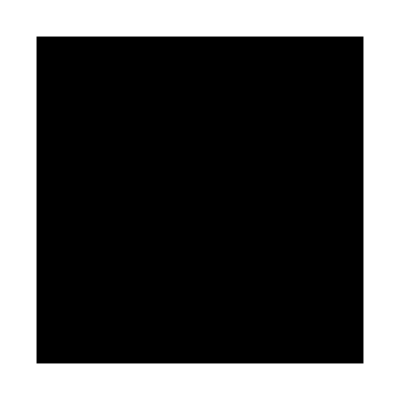

```mathematica
Graphics[Polygon[{{0,0},{0,1},{1,1},{1,0}}]]
```

```mathematica
wheelLayout[shapes_,epsilon_]:=Module[{
positions,count=Length@shapes,
maxH,maxW,max,r},
maxH=Max[Map[#⟦1⟧&,shapes]];
maxW=Max[Map[#⟦2⟧&,shapes]];
max=Max[maxH,maxW];
r=(1+epsilon)*max *count/(2Pi);
positions=Map[
r{Cos[2Pi #/(count+1)],Sin[2Pi #/(count+1)]}&,
Range[0,count-1]];
positions]
```

```mathematica
randomBlob:={1,.618};
```

```mathematica
blob[{h_,w_}]:={randCol,Polygon[{{-w/2,-h/2},{-w/2,h/2},{w/2,h/2},{w/2,-h/2}}]}
```

```mathematica
blobExp[n_,eps_]:=With[{rs=Table[randomBlob,{n}]},
Graphics[MapThread[
GeometricTransformation[blob[#1],
TranslationTransform[#2]]&,{rs,wheelLayout[rs,eps]}],
AspectRatio->1]]
```

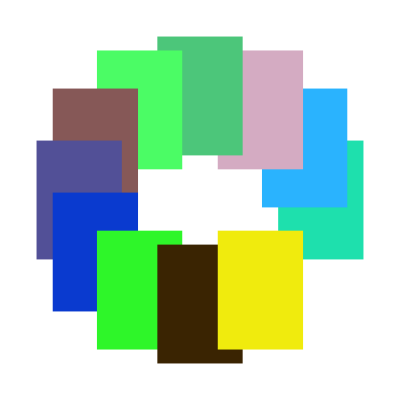

```mathematica
blobExp[11,-0.5]
```

## Tweening

```mathematica
linSamp[p1_,p2_,nLegs_]:=Table[p1+t*(p2-p1),{t,0,1,1/nLegs}]
```

```mathematica
quadSamp[p1_,p2_,nLegs_]:=Module[{
dx=p2⟦1⟧-p1⟦1⟧,
dy=p2⟦2⟧-p1⟦2⟧,
vt,
vx,vy,
wy,
us},
vt=Table[t,{t,0,1,1/nLegs}];
(* have these calc the function you want *)
vx=2vt-1;
vy=1-vx^2;
(* have these mapped back to {0,1} in x 
and whatever you want in y *)
wy=vy/2;
us=MapThread[
Function[{x,y},p1+{x dx-y dy,x dy+y dx,0}],
{vt,wy}]]
```

```mathematica
sinSamp[p1_,p2_,nLegs_]:=Module[{
dx=p2⟦1⟧-p1⟦1⟧,
dy=p2⟦2⟧-p1⟦2⟧,
vt,
vx,vy,
wx,wy,
us},
vt=Table[t,{t,0,1,1/nLegs}];
(* have these calc the function you want *)
vx=4 Pi vt;
vy=Sin[vx]/(4Pi);
(* have these mapped back to {0,1} in x 
and whatever you want in y *)
wy=vy;
us=MapThread[
Function[{x,y},p1+{x dx-y dy,x dy+y dx,0}],
{vt,wy}]]
```

```mathematica
sinSamp[{0,0,0},{1,0,0},9]
```

(0 | 0 | 0
1/9 | (cos(π/18))/(4 π) | 0
2/9 | (sin(π/9))/(4 π) | 0
1/3 | -(√3)/(8 π) | 0
4/9 | -(sin((2 π)/9))/(4 π) | 0
5/9 | (sin((2 π)/9))/(4 π) | 0
2/3 | (√3)/(8 π) | 0
7/9 | -(sin(π/9))/(4 π) | 0
8/9 | -(cos(π/18))/(4 π) | 0
1 | 0 | 0)

```mathematica
Module[{rg={{-10,-10},{10,10}},fz},
fz=Function[p2D,p2D~Join~{0}];
Manipulate[
Show[
Graphics3D@Text[u,{u⟦1⟧,u⟦2⟧-1,0}],
Graphics3D@Text[b,{b⟦1⟧,b⟦2⟧-1,0}],
Graphics3D@Line@sinSamp[fz@u,fz@b,28],
ball2[u,{randCol}],
ball2[b],
PlotRange->10,
AxesLabel->{"X","Y","Z"},
Axes->True,
Boxed->True,
ViewPoint->{0,0,∞}],
{{u,{0,0},"u"},Sequence@@rg},
{{b,{4,7},"b"},Sequence@@rg},
ControlPlacement->Left
]]
```

Parabolic Tweening

```mathematica
parabolicTween[tIn_, p1_, p2_]:=Module[{
t1=If[tIn≠0&&(tIn==Floor[tIn]),1, Mod[tIn,1]],
d=EuclideanDistance[p1,p2],
vx,vy,
dx,dy},
vx=2*t1-1;
vy=(1-vx^2);
dx=p2⟦1⟧-p1⟦1⟧;
dy=p2⟦2⟧-p1⟦2⟧;
(p2-p1)/2+
((1/2)*{dx vx-dy vy,dy vx+dx vy}+
p1)]
```

```mathematica
N@parabolicTween[#,
{0,-1},{0,1}]&/@Prepend[Range[10]/10,0]
```

(0. | -1.
-0.36 | -0.8
-0.64 | -0.6
-0.84 | -0.4
-0.96 | -0.2
-1. | 0.
-0.96 | 0.2
-0.84 | 0.4
-0.64 | 0.6
-0.36 | 0.8
0. | 1.)

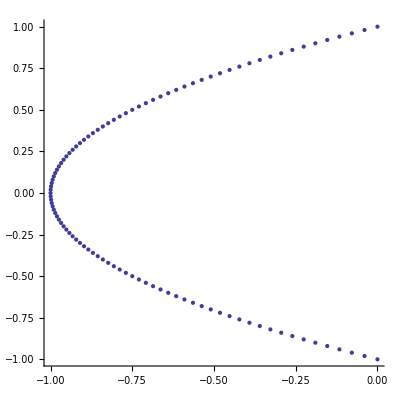

```mathematica
ListPlot[
parabolicTween[#,
{0,-1},{0,1}]&/@Prepend[Range[100]/100,0],
PlotRange->2,
AspectRatio->1]
```

Bugbug?

```mathematica
If[#≠0&&(#==Floor[#]),1, Mod[#,1]]&/@Prepend[Range[10]/10,0]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
If[#≠0&&(#==Floor[#]),1, Mod[#,1]]&[Prepend[Range[10]/10,0]]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,0}

```mathematica
If[#≠0&&(#==Floor[#]),1, Mod[#,1]]&/@{1}
```

{1}

```mathematica
f[x_]:=(x==Floor[x]);
```

```mathematica
Floor[{0}]
```

{0}

```mathematica
Floor[{0,1}]
```

{0,1}

```mathematica
Floor[{0,1/2,1}]
```

{0,0,1}

```mathematica
f[{0}]
```

True

```mathematica
f[{0,1}]
```

True

```mathematica
f[{0,1/2,1}]
```

False

```mathematica
If[#≠0&&(#==Floor[#]),1, Mod[#,1]]&[{0,1/2,1}]
```

{0,1/2,0}

## Particles in a box

One-body Problem in the Plane

```mathematica
G=1;
```

Let the state vector be {x_1,y_1,OverDot[x_1],OverDot[y_1]}

Let c contain the coordinates of the fixed force center.

Prophylaxis

Compare with another demonstration, this one from http://www.artcompsci.org/

```mathematica
eulerStep[ψ_,ϕ_,t_,dt_]:=Module[{dtk1=dt*ϕ[ψ,t].ψ},ψ+dtk1]
```

```mathematica
gravsMat[ψ_,c_,m1_,m2_]:=Module[{rCubed=EuclideanDistance[{ψ⟦1⟧,ψ⟦2⟧},c]^3},
{(* velocity section *)
{0,0,1,0},{0,0,0,1},
(* acceleration section *)
{G m1 m2 If[ψ⟦1⟧≠0,(c⟦1⟧-ψ⟦1⟧)/(ψ⟦1⟧rCubed),0],0,0,0},
{0,G m1 m2 If[ψ⟦2⟧≠0,(c⟦2⟧-ψ⟦2⟧)/(ψ⟦2⟧rCubed),0],0,0}}   ]
```

```mathematica
takeEveryNth[l_List,n_Integer]:=Table[l⟦i⟧,{i,1,Length[l],n}]
```

```mathematica
run[algo_,nStepsExp_,init_]:=takeEveryNth[
Module[{
dt=0.01/10^(nStepsExp-3), (* time step *)
t0=0., (* start time *)
tN=10., (* end time *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
ϕ=Function[{q,t},gravsMat[q,{0,0},1,1]];
FoldList[
algo[#1,ϕ,#2,dt]&,(* calculate one step *)
init,(* initial state *)
Range[t0,tN,dt]]],10^(nStepsExp-3+1)]
```

```mathematica
(Timing[gravsSol=run[eulerStep,3,{1,0,0,1}]]⟦1⟧//ToString)<>" seconds to solve."
```

0.078 seconds to solve.

```mathematica
Length@gravsSol
```

101

```mathematica
Take[gravsSol,5]~Join~{{"-","-","-","-"}}~Join~Take[gravsSol,-5]
```

(1 | 0 | 0 | 1
0.995504 | 0.0998801 | -0.0998126 | 0.995506
0.981065 | 0.198863 | -0.198578 | 0.981086
0.956834 | 0.295963 | -0.295308 | 0.956903
0.923057 | 0.390215 | -0.389037 | 0.923224
- | - | - | -
-0.737136 | 0.883513 | -0.733982 | -0.584439
-0.808304 | 0.822511 | -0.683619 | -0.640498
-0.874245 | 0.756103 | -0.62912 | -0.692052
-0.934566 | 0.684753 | -0.570903 | -0.738816
-0.988915 | 0.608951 | -0.509405 | -0.780544)

```mathematica
showSol[g_,r_]:=ListPlot[Transpose[{g⟦All,1⟧,g⟦All,2⟧}],PlotRange->r,AspectRatio->1]
```

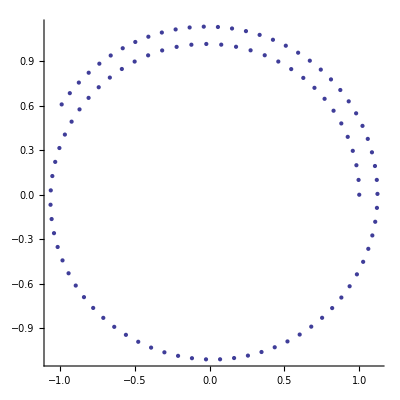

```mathematica
showSol[gravsSol,1.5]
```

Bingo! gaining energy, just like figure 20 (or 7.3 in the pdf version) in http://www.artcompsci.org/kali/pub/msa/title.html

```mathematica
(Timing[gravsSol=run[eulerStep,3,{1,0,0,0.5}]]⟦1⟧//ToString)<>" seconds to solve."
```

0.078 seconds to solve.

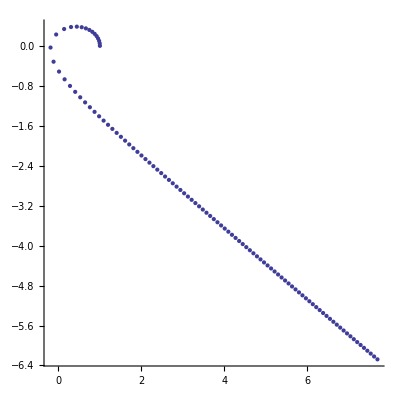

```mathematica
showSol[gravsSol,8]
```

```mathematica
(Timing[gravsSol=run[eulerStep,4,{1,0,0,0.5}]]⟦1⟧//ToString)<>" seconds to solve."
```

0.687 seconds to solve.

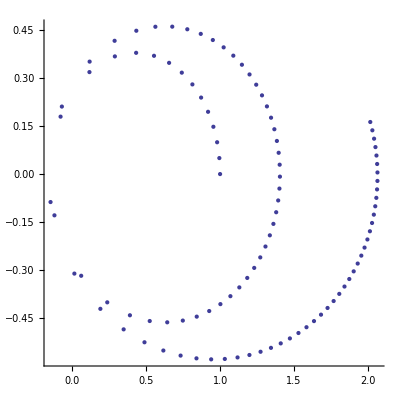

```mathematica
showSol[gravsSol,3]
```

```mathematica
(Timing[gravsSol=run[eulerStep,4,{1,0,0,1}]]⟦1⟧//ToString)<>" seconds to solve."
```

0.687 seconds to solve.

Here's the web site's figure 21 http://www.artcompsci.org/kali/pub/msa/ch08.html

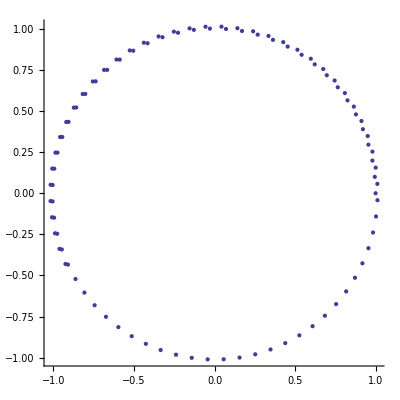

```mathematica
showSol[gravsSol,3/2]
```

```mathematica
(Timing[gravsSol=run[eulerStep,5,{1,0,0,0.5}]]⟦1⟧//ToString)<>" seconds to solve."
```

6.817 seconds to solve.

Here's the web site's figure 24 http://www.artcompsci.org/kali/pub/msa/ch08.html

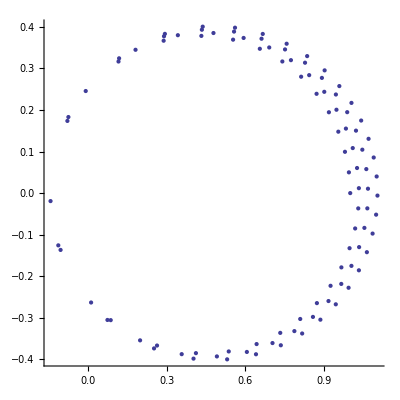

```mathematica
showSol[gravsSol,3/2]
```

```mathematica
(Timing[gravsSol=run[eulerStep,6,{1,0,0,0.5}]]⟦1⟧//ToString)<>" seconds to solve."
```

71.464 seconds to solve.

Here's the web site's figure 25 http://www.artcompsci.org/kali/pub/msa/ch08.html

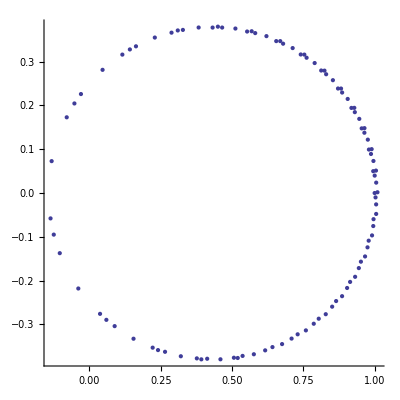

```mathematica
showSol[gravsSol,3/2]
```

Nicer Display

```mathematica
Module[{rg={{-10,-10},{10,10}}},
Manipulate[
Show[
ball2[u,{randCol}],
ball2[b],
PlotRange->10,
AxesLabel->{"X","Y","Z"},
Axes->True,
Boxed->True,
ViewPoint->{0,0,∞}],
{{u,{0,0},"foo"},Sequence@@rg},
{{b,{4,7},"bar"},Sequence@@rg},
ControlPlacement->Left
]]
```

## Old-Style Beads Solution (Junkyard)

## Solution and Equations in One Step

```mathematica
solArr=((NDSolve[{
((gravf[θ1[t]]+spinf[θ1[t],Ω]+dampf[θ1'[t]]
-ef[θ2[t],θ1[t]]
-ef[θ3[t],θ1[t]]
-ef[θ4[t],θ1[t]]
-ef[θ5[t],θ1[t]]
-ef[θ6[t],θ1[t]]
-ef[θ7[t],θ1[t]])/(m R^2)
==θ1''[t])/.Ω:>#,
θ1'[0]==θ1dot0,θ1[0]==θ10,
((gravf[θ2[t]]+spinf[θ2[t],Ω]+dampf[θ2'[t]]
-ef[θ4[t],θ2[t]]
-ef[θ3[t],θ2[t]]
-ef[θ1[t],θ2[t]]
-ef[θ5[t],θ2[t]]
-ef[θ6[t],θ2[t]]
-ef[θ7[t],θ2[t]])/(m R^2)
==θ2''[t])/.Ω:>#,
θ2'[0]==θ2dot0,θ2[0]==θ20,
((gravf[θ3[t]]+spinf[θ3[t],Ω]+dampf[θ3'[t]]
-ef[θ4[t],θ3[t]]
-ef[θ1[t],θ3[t]]
-ef[θ2[t],θ3[t]]
-ef[θ5[t],θ3[t]]
-ef[θ6[t],θ3[t]]
-ef[θ7[t],θ3[t]])/(m R^2)
== θ3''[t])/.Ω:>#,
θ3'[0]==θ3dot0,θ3[0]==θ30,
((gravf[θ4[t]]+spinf[θ4[t],Ω]+dampf[θ4'[t]]
-ef[θ1[t],θ4[t]]
-ef[θ2[t],θ4[t]]
-ef[θ3[t],θ4[t]]
-ef[θ5[t],θ4[t]]
-ef[θ6[t],θ4[t]]
-ef[θ7[t],θ4[t]])/(m R^2)
== θ4''[t])/.Ω:>#,
θ4'[0]==θ4dot0,θ4[0]==θ40,
((gravf[θ5[t]]+spinf[θ5[t],Ω]+dampf[θ5'[t]]
-ef[θ1[t],θ5[t]]
-ef[θ2[t],θ5[t]]
-ef[θ3[t],θ5[t]]
-ef[θ4[t],θ5[t]]
-ef[θ6[t],θ5[t]]
-ef[θ7[t],θ5[t]])/(m R^2)
== θ5''[t])/.Ω:>#,
θ5'[0]==θ5dot0,θ5[0]==θ50,
((gravf[θ6[t]]+spinf[θ6[t],Ω]+dampf[θ6'[t]]
-ef[θ1[t],θ6[t]]
-ef[θ2[t],θ6[t]]
-ef[θ3[t],θ6[t]]
-ef[θ4[t],θ6[t]]
-ef[θ5[t],θ6[t]]
-ef[θ7[t],θ6[t]])/(m R^2)
== θ6''[t])/.Ω:>#,
θ6'[0]==θ6dot0,θ6[0]==θ60,
((gravf[θ7[t]]+spinf[θ7[t],Ω]+dampf[θ7'[t]]
-ef[θ1[t],θ7[t]]
-ef[θ2[t],θ7[t]]
-ef[θ3[t],θ7[t]]
-ef[θ4[t],θ7[t]]
-ef[θ5[t],θ7[t]]
-ef[θ6[t],θ7[t]])/(m R^2)
== θ7''[t])/.Ω:>#,
θ7'[0]==θ7dot0,θ7[0]==θ70
},
{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t],θ7[t]},{t,lowT,highT},
Method->"StiffnessSwitching",
MaxSteps->20000]& )
/@ Ωs)//Flatten;
```

```mathematica
sol[k_,Ω_]:=solArr⟦k+7Floor[Ω/incrΩ]⟧;
```

```mathematica
pick[k_]:=Switch[k,1,θ1[t],2,θ2[t],3,θ3[t],4,θ4[t],5,θ5[t],6,θ6[t],7,θ7[t]];
```

```mathematica
theta[k_,Om_,a_]:=pick[k]/.sol[k,Om]/.t->a;
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
thetaDot[k_,Om_,a_]:=ND[(pick[k]/.sol[k,Om]),t,a];
```

## Plots

Somehow, 't' is visible in thetaDot and the plot variable must NOT be 't'.

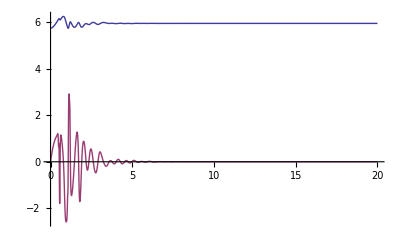

```mathematica
Plot[{
theta[2,.8,z],
thetaDot[2,.8,z]},
{z,lowT,highT}]
```

## Animation

```mathematica
Module[{},
Manipulate[
Show[
(* This one is hard to reverse-engineer -- see above 
MapAt[RotationTransform[ Om a,{0,0,1}],
ring,{
{1,1},(* body of the ring *)
{1,3,2} (* the lights *)
}],*)
ring,
frame,
ball[theta[1,#1,#2]&,Om,a,randCol],
ball[theta[2,#1,#2]&,Om,a,col2],
ball[theta[3,#1,#2]&,Om,a,col3],
ball[theta[4,#1,#2]&,Om,a,col4],
ball[theta[5,#1,#2]&,Om,a,col5],
ball[theta[6,#1,#2]&,Om,a,col6],
ball[theta[7,#1,#2]&,Om,a,col7],
minotaur[Om,a],
Boxed->True,
Axes->True,
AxesLabel->{"X","Y","Z"},
ViewPoint->{0,-∞,0},PlotRange->1.2,ImageSize->{400,400}],{{a,0,"animate"},0,4 π,.005(4 π),ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->False,AnimationRate->14},
{{a,0,"manual control"},0,4 π,.005(4 π)},
{{Om,0,"rotation frequency"},0.,topΩ,incrΩ},
Initialization:>{},
AutorunSequencing->{{2,30}},
TrackedSymbols->Manipulate]]
```